## Naloga 3

Sestavite funkcijo sedla[m_], kot je zapisano v navodilih.

```mathematica
vsiIndeksi[n_,m_]:=Flatten[Table[{i,j},{i,1,n},{j,1,m}],1]
maxVrstice[m_]:=Map[Max,m]
minStolpca[m_]:=Map[Min,Transpose[m]]
sedla[a_]:=With[{n=Length[a],m=Length[a[[1]]],maxVr=maxVrstice[a],minSt=minStolpca[a]},Select[vsiIndeksi[m,n],a[[#[[1]],#[[2]]]]==maxVr[[#[[1]]]]==minSt[[#[[2]]]]&]]
```

```mathematica
sedla[{{1, 2, 3},{4, 5, 6},{1, 2, 3}}]
```

{{1,3},{3,3}}

## Naloga 4

Sestavite funkcijo hiperkocka[n_], kot je zapisano v navodilih.

```mathematica
PolarToCartesian[{r_,fi_}]:={r*Cos[fi],r*Sin[fi]}
tocke[n_]:=PolarToCartesian[{1,2*Pi*#/2^n}]&/@Range[0,2^n-1]
hammingEna[p_]:=With[{i=p[[1]],j=p[[2]]},Plus@@IntegerDigits[BitXor[i,j],2]==1]
povezave[n_]:=Select[Subsets[Range[0,2^n-1],{2}],hammingEna]
hiperkocka[n_]:=With[{t=tocke[n],p=povezave[n]},Graphics[{Line[{t[[#[[1]]+1]],t[[#[[2]]+1]]}]&/@p,PointSize[Large],Point/@t}]]
```

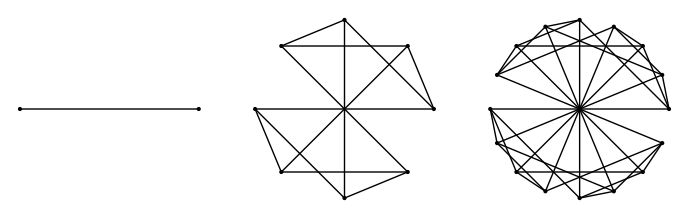

```mathematica
GraphicsRow[{hiperkocka[1],hiperkocka[3],hiperkocka[4]}]
```